# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
data=Map[{#[[1]]*10^(-6), #[[2]]*10^5, #[[3]]}&,data,{2}];
```

## Plotting

```mathematica
(*a0=0.8405;
b0=9.397/10^5;
n0=1.330/10^3;*)
R=8.314;
```

```mathematica
a0=0.7823989059663622;
b0=0.00008552182664372191;
n0=0.0013382362023847158;
```

```mathematica
(*a0=0.7790376551106099;
b0=8.61257*10^(-5);
n0=1.35069*10^(-3);*)
```

```mathematica
indices={1,3,5,9,13}
```

{1,3,5,9,13}

```mathematica
temps[[indices]]
```

{30.1,35.,40.1,45.1,50.2}

```mathematica
8a0/(27 R b0)-273.15
```

52.8874

## Maxwell’s Construction

```mathematica
intersectionPoints[Pval_,T0_]:=Sort[Flatten[Values[Solve[(n0 R T0)/(V-n0 b0)-(n0^2 a0)/V^2==Pval,V]]]]
```

```mathematica
area[Pval2_,T0_]:=With[{vals =intersectionPoints[Pval2,T0]},Integrate[(n0 R T0)/(V-n0 b0)-(n0^2 a0)/V^2-Pval2,{V,vals[[1]],vals[[3]]}]]
```

```mathematica
findHeight[T0_,toler_:1]:=Module[{min=500000,max=10^7,mid,intpts},While[Abs[max-min]>toler, mid=(max+min)/2; intpts=intersectionPoints[mid,T0];If[RealValuedNumberQ[intpts[[1]]]&&Not[RealValuedNumberQ[intpts[[3]]]],max=mid,If[RealValuedNumberQ[intpts[[3]]]&&Not[RealValuedNumberQ[intpts[[1]]]],min=mid,If[area[mid,T0]<0,max=mid, min=mid]]]];mid]
```

```mathematica
heights=findHeight[temps[[#]]+273.15]&/@indices;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
intersectionPoints[heights[[2]],temps[[indices[[2]]]]+273.15]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{2.31347×10^-7,3.59443×10^-7,6.12381×10^-7}

```mathematica
temps[[indices]]
```

{30.1,35.,40.1,45.1,50.2}

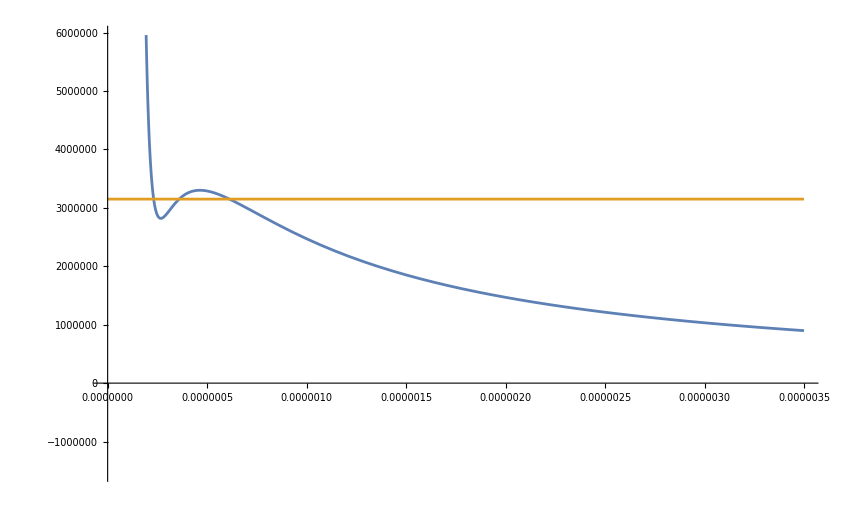

```mathematica
Plot[{(n0 R (35+273.15))/(V-n0 b0)-(n0^2 a0)/V^2, heights[[2]]},{V,0,3.5*10^(-6)}]
```

## How many need the cutoff?

```mathematica
cutoff=5;
```

```mathematica
funcLst1=Table[With[{vals=intersectionPoints[heights[[i]],temps[[indices[[i]]]]+273.15],temp=temps[[indices[[i]]]]+273.15,height=heights[[i]]},Function[V,Piecewise[{{height,vals[[1]]<=V<=vals[[3]]}},(n0 R temp)/(V-n0 b0)-(n0^2 a0)/V^2]]],{i,1,cutoff}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
funcLst2=Table[With[{temp=temps[[indices[[i]]]]+273.15},Function[V,(n0 R temp)/(V-n0 b0)-(n0^2 a0)/V^2]],{i,cutoff+1,Length[indices]}]
```

{}

```mathematica
funcLst=Join[funcLst1,funcLst2];
```

```mathematica
funcLst[[1]][0.1]
```

33.7398

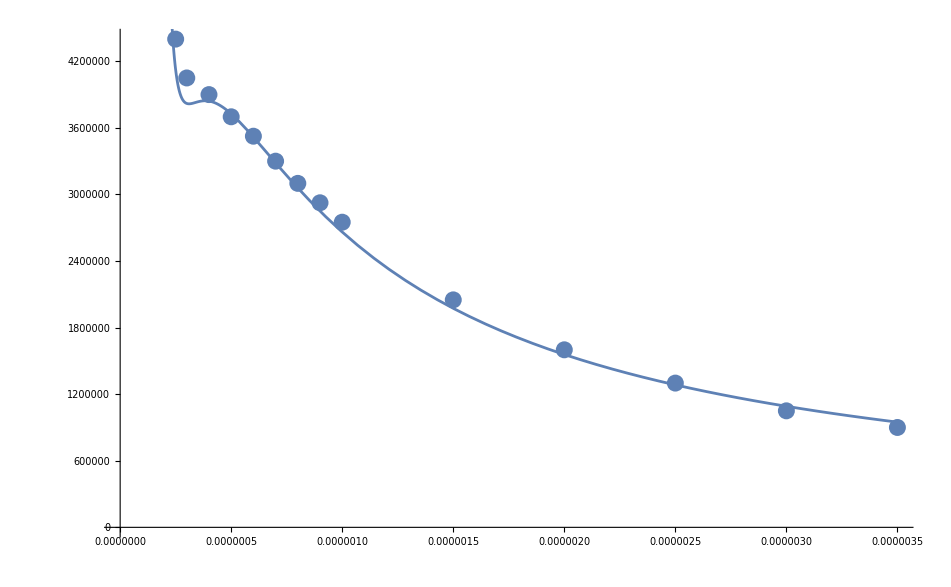

```mathematica
Show[ListPlot[data[[-1,All,{1,2}]]],Plot[(n0 R (temps[[-1]]+273.15))/(V-n0 b0)-(n0^2 a0)/V^2,{V,0,3.5*10^(-6)}]]
```

```mathematica
data[[-1]]==data[[indices[[-1]]]]
```

True

## plot

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
Show[ListPlot[data[[#,All,{1,2}]]&/@indices,PlotStyle->cols[[indices]],PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}],pltsettings],Plot[Evaluate[#[t]&/@funcLst],{t,0,3.5*10^(-6)},PlotStyle->cols[[indices]]]]
```

-Graphics-

```mathematica
Show[ListPlot[Map[{#[[1]]*10^6,#[[2]]*10^(-6)}&,data[[#,All,{1,2}]]&/@indices,{2}],PlotStyle->cols[[indices]],PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}],pltsettings],Plot[Evaluate[10^(-6)#[t*10^(-6)]&/@funcLst],{t,0,3.5},PlotStyle->cols[[indices]]]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig5.pdf",Show[ListPlot[Map[{#[[1]]*10^6,#[[2]]*10^(-6)}&,data[[#,All,{1,2}]]&/@indices,{2}],PlotStyle->cols[[indices]],PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}],pltsettings],Plot[Evaluate[10^(-6)#[t*10^(-6)]&/@funcLst],{t,0,3.5},PlotStyle->cols[[indices]]]],Background->None];
```

```mathematica
Plot[f1[t],{t,0,3.5*10^(-6)}]
```

-Graphics-